# Defect Modular Bootstrap

## When the modular matrix has degeneracies modular bootstrap can only do so much to predict the the topological lines of the theory. Here we use a version of Breadth First Search to resolve the ambiguities.

## Modular Bootstrap

We will do this example on the folded Tricritical Ising CFT, but the parameters will be documented so that one can change them.

### Defining Folded Tricritical Ising Modular Data

```mathematica
(* Autosave because I've been burnt before *)
SetOptions[$FrontEnd,AutoSaveFrequency->1];
Get[FileNameJoin[{NotebookDirectory[],"math4ti2.m"}]];

(* A Timing Function *)
SetAttributes[Time,HoldFirst]
Time[x_]:=With[{res=AbsoluteTiming[x]},Echo[res[[1]],"Time: "];res[[2]]];

(* Define Tricritical Ising Parameters *)
FoldedMinimalModularData[p_:5,pp_:4]:= Module[
{cv,hv,sv,tv,H,i,ho,t,sMaker,s,nH,HIndex,svMat,tv2,twist},
cv=1-6(p-pp)^2/(p pp);(*//Echo[#,"c = "]&;*)
hv[r_,s_]:=hv[r,s]=((p r - pp s)^2-(p - pp)^2)/(4 p pp);
sv[a_,b_]:=sv[a,b]=2 (2/(p pp))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/pp a[[1]] b[[1]]]Sin[π pp/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=tv[a,e]=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(pp-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[pp], Table[{pp/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];

(* Labels of folded Minimal Model primaries under the fixed point chiral algebra *)
i=({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^#}& /@Range[2,2Length[H]+1])~Join~({#[[1]],#[[2]],0}&/@Subsets[H,{2}])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^# 2}& /@Range[2,2Length[H]+1]);

(* Their Conformal Weights *)
ho[a_]:=ho[a]=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;

(* Modular T-Matrix *)
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;

(*── Precomputed sv/tv tables for H×H ──────────────────────────────*)
nH=Length[H];
HIndex=AssociationThread[H->Range[nH]];
svMat=Table[sv[H[[a]],H[[b]]],{a,nH},{b,nH}];
tv2=Table[tv[H[[a]]]^2,{a,nH}];
twist[a1_,b1_]:=twist[a1,b1]=svMat[[HIndex[a1]]].(tv2*svMat[[All,HIndex[b1]]]);

(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:=sMaker[a,b]=Module[
{a1=a[[1]],a2=a[[2]],a3=a[[3]],b1=b[[1]],b2=b[[2]],b3=b[[3]]},
Which[a3==0&&b3==0,sv[a1,b1] sv[a2,b2]+sv[a1,b2] sv[a2,b1],
a3==0&&Abs[b3]==1,sv[a1,b1] sv[a2,b1],
Abs[a3]==1&&b3==0,sv[a1,b1] sv[a1,b2],
Abs[a3]==1&&Abs[b3]==1,1/2 sv[a1,b1]^2,
Abs[a3]==1&&Abs[b3]==2,1/2 a3 sv[a1,b1],
Abs[a3]==2&&Abs[b3]==1,1/2 b3 sv[a1,b1],
Abs[a3]==2&&Abs[b3]==2,1/8 a3 b3 twist[a1,b1] Exp[π ⅈ (hv@@a1+hv@@b1-cv/12)],
True,0]
];

s=Simplify[Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}],ComplexityFunction->LeafCount];
{s,t,i}
];
{s,t,i}=(Clear[s,t,i];FoldedMinimalModularData[5,4])//Time;

(* Modular Mass Matrix *)
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
MatrixPlot[z,PlotLabel->"Modular Mass Matrix z"]
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

Time:   0.719923

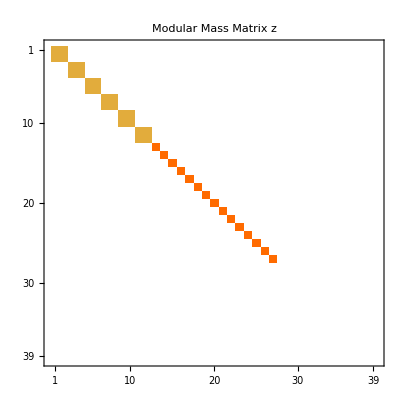

### Obtaining Modular Bootstrap Equations

```mathematica
SolveModularBootstrap[z_,s_]:=Module[
{X,x,nz, st=ConjugateTranspose[s],m,coeff,A, eqn,multipliers,basis},
Needs["math4ti2`"];

(* Get Nonzero positions on the Mass Matrix and replace them with variables *)
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=st. ReplacePart[z,Thread[nz->X]] . s//Flatten;

(* Extract the coefficients for each variable in the S transformed Mass Matrix *)
coeff= CoefficientArrays[m,X][[2]]//Normal//N//Chop;

(* Pick the maximum number of independent equations and invert them *)
A=Chop@Inverse@N@coeff[[Flatten[FirstPosition[#,1]&/@DeleteCases[Chop@RowReduce@N@Transpose@coeff,{0..}]]]];

(* Plug them back in to the S-Transformed Modular Matrix to obtain constraints *)
m=Chop[N[coeff.A]].X;
A=RootApproximant[A];
eqn=DeleteDuplicates@Rationalize@Chop@Expand[#>=0&/@m];

(* Rescale any variables that need it so that the system has integer coefficients *)
multipliers=Min@Cases[eqn,(a_.*#)>=0:>a]^-1&/@X;
eqn=(#[[0]][Subtract@@#//ExpandAll,0])&/@(eqn/. Thread[X->multipliers*X]);

(* Use Z-Solve to find a basis of simple objects *)
basis =math4ti2`zsolve[eqn][[2]];

A. (multipliers*#)&/@basis //FullSimplify
];
families=Sort[SolveModularBootstrap[z,s],#1[[1]] <= #2[[1]]&];//Time
families//Transpose//MatrixForm
noninvertibleFamilies=Select[families,#[[1]]!=1&];
```

Time:   2.86752

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | -2 (3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | √(3+√5) | √(3-√5) |  | -√(3+√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | 2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 (-3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) |  | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | √(3-√5) |  | √(3-√5) |  | 0 | -3+√5 | 3-√5 | 0 | 0 | √(7-3 √5) | (-3+√5)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 |  | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 |  | √(3-√5) |  | √(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | (-3+√5)/(√2) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | -√(3+√5) |  | √(3-√5) | √(3+√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Resolving Ambiguities

As we can see from the answers above for part of the primaries the action of the defects is ambiguous and we really only know the trace. Yet we have a lot of data, perhaps enough to fully constrain the action on the primaries (up to a basis choice). To do this we will use fusion rules. These are highly constrained also simply by looking at the action in the nondegenerate primaries. Then we will search fusion rules for consistencies using a version of BFS.

### Defect Manipulations

Since we don’t need a really big matrix to store the action of the defects, we will instead opt to store them using a list of 1x1 and 2x2 matrices depending on which are ambiguous or not. So we can define an associative operation for the tensor product!!

```mathematica
(* Define a Defect Fusion Product Operation *)
SetAttributes[CircleTimes,{Flat,OneIdentity}]
a_ ⊗ b_:=MapThread[Which[MatrixQ[#1]&&MatrixQ[#2],#1.#2,True,#1*#2]&,{a,b}];
CircleTimes[a_,b_,rest__]:=CircleTimes[CircleTimes[a,b],rest]

(* A couple of helper functions that can be applied to Lines *)
tr[x_]:=Which[MatrixQ[x],Tr[x],True,x];
inv[x_]:=Which[MatrixQ[x],Inverse[x],True,1/x];
dual[x_]:=Which[MatrixQ[x],ConjugateTranspose[x],True,Conjugate[x]];
SuperDagger[x_]:=dual/@x;
ShowLine[L_]:=MatrixForm[MatrixForm/@L];

(* This mask tells us if the current primary is degenerate *)
degMask=Thread[families[[1]]!=1];
degPos=Flatten@Position[degMask,True];
nondegPos=Flatten@Position[Not/@degMask,True];
deg[x_]:=degMask[[x]];
degNum=Total@Boole@degMask;
primNum=Total@Boole@degMask;
famNum=Length@families;
familiesNondeg=families[[All,nondegPos]];degeneracy[i_Integer]:=families[[1,i]];
```

### Invertible Lines

```mathematica
GetInvertibleLines[]:=Module[
{i={{1,0},{0,1}},
a={{1,0},{0,-1}},
b={{0,1},{1,0}},
c={{0,1},{-1,0}},
L1,Lσ,Lχ},
L1={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,i,i,i,i,i,i,i,i,i,i,i,i,i,i};
Lσ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a};
Lχ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,a,a,a,c,c,a,a,c,c,a,c,c,c,c,-a};
{L1,Lχ⊗Lχ,Lχ⊗Lσ,Lσ⊗Lχ,Lσ,Lσ⊗Lχ⊗Lχ,Lχ,Lχ⊗Lχ⊗Lχ}
];

(* Extract the invertible Lines *)
Li=GetInvertibleLines[];
L=GetInvertibleLines[];
solvedFamilies=<|
1->{Li[[1]]},
2->{Li[[2]]},
3->Li[[3;;4]],
4->Li[[5;;6]],
5->Li[[7;;8]]
|>;
SolvedQ[x_Integer]:=KeyExistsQ[solvedFamilies,x];

(* Functions to create a defect with free variables and given traces, as well to extract the variables *)
(*l[traces_,var_]:= Array[Which[!deg[#],traces[[#]],deg[#],{{var[#,1]+ⅈ var[#,2] ,var[#,3]+ⅈ var[#,4] },{var[#,5]+ⅈ var[#,6],traces[[#]]-var[#,1]-ⅈ var[#,2]}}]&,Length@traces];*)
l[var_Symbol]:=Array[Module[{n=degeneracy[#]},Which[n==1,var[#],True,Table[var[#,n*i + j -2],{i,n},{j,n}]]]&,famNum] ;
l[traces_List,var_]:= Array[Which[!deg[#],traces[[#]],deg[#],{{var[#,1] ,var[#,2]},{var[#,3],traces[[#]]-var[#,1]}}]&,Length@traces];
getVars[x_]:=x//Flatten//Variables;
```

### Gauge Fixing

```mathematica
(* Obtain a general Gauge Transformation that preserves the solved Lines *)
gaugeVars= getVars[L];
gaugeVarRules=Thread[gaugeVars!=0];
GetGeneralGaugeTransform[L_,gaugeVars_,gaugeVarRules_,var_:P]:=Module[{Lp,LpInvertibleQ,Lpp},
(* Build a General Gauge Transformation *)
Lp=Array[Which[!deg[#],1,deg[#],{{var[#,1] ,var[#,2] },{var[#,3],var[#,4]}}]&,famNum];
Lp=(Lp //.{Assuming[gaugeVarRules,ToRules[Reduce[And@@Thread[Flatten[(Lp⊗# -#⊗Lp)&/@L]==0],Backsubstitution->True]]]});
Lpp=DeleteElements[Variables[Lp],gaugeVars];

(* Checks if Lp is invertible for a given numerical set of P variables *)
Module[{
vars=Table[Unique["p"],Length@Lpp],
varsg=Table[Unique["g"],Length@gaugeVars],
invertibleLp=And@@((Simplify@Not@Reduce[Or@@(Which[MatrixQ[#],Det[#]==0,True,#==0]&/@#)])&/@Lp)
},
invertibleLp=invertibleLp/.Thread[Lpp->vars]/.Thread[gaugeVars->varsg];
LpInvertibleQ:=Function@@{vars,Assuming[gaugeVarRules/.Thread[gaugeVars->varsg],Simplify[Evaluate[invertibleLp]]]}
];
{Lp,Lpp,LpInvertibleQ}
];
{Lp,Lpp,LpInvertibleQ}=GetGeneralGaugeTransform[L,gaugeVars,gaugeVarRules,P]
```

{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,{{P[25,1],0},{0,P[25,4]}},{{P[26,1],0},{0,P[26,4]}},{{P[27,1],0},{0,P[27,4]}},{{P[28,4],0},{0,P[28,4]}},{{P[29,4],0},{0,P[29,4]}},{{P[30,1],0},{0,P[30,4]}},{{P[31,1],0},{0,P[31,4]}},{{P[32,4],0},{0,P[32,4]}},{{P[33,4],0},{0,P[33,4]}},{{P[34,1],0},{0,P[34,4]}},{{P[35,4],0},{0,P[35,4]}},{{P[36,4],0},{0,P[36,4]}},{{P[37,4],0},{0,P[37,4]}},{{P[38,4],0},{0,P[38,4]}},{{P[39,1],0},{0,P[39,4]}}}},{P[25,1],P[25,4],P[26,1],P[26,4],P[27,1],P[27,4],P[28,4],P[29,4],P[30,1],P[30,4],P[31,1],P[31,4],P[32,4],P[33,4],P[34,1],P[34,4],P[35,4],P[36,4],P[37,4],P[38,4],P[39,1],P[39,4]},Function[{p11,p12,p13,p14,p15,p16,p17,p18,p19,p20,p21,p22,p23,p24,p25,p26,p27,p28,p29,p30,p31,p32},p11≠0&&p12≠0&&p13≠0&&p14≠0&&p15≠0&&p16≠0&&p17≠0&&p18≠0&&p19≠0&&p20≠0&&p21≠0&&p22≠0&&p23≠0&&p24≠0&&p25≠0&&p26≠0&&p27≠0&&p28≠0&&p29≠0&&p30≠0&&p31≠0&&p32≠0]}

```mathematica
(* These are Queries for if a line is related by conjugation of invertible defects, or by a change of Gauge, or both *)
Clear[conjugateOrbit,NconjugateOrbit,leftOrbit,rightOrbit,gaugeNullSpace,fusionOrbit];
conjugateOrbit[x_,Li_:Li,gaugeVarRules_:gaugeVarRules]:=conjugateOrbit[x,Li,gaugeVarRules]=DeleteDuplicates[Simplify[#⊗x⊗(inv/@#),Assumptions->gaugeVarRules]&/@Li];
fusionOrbit[x_,L_:L]:=fusionOrbit[x,L]=DeleteDuplicates[Simplify[Flatten[Outer[#1⊗x⊗#2&,L,L,1,1],1]]];
NconjugateOrbit[x_,Li_:Li,gaugeVarRules_:gaugeVarRules]:=NconjugateOrbit[x]=DeleteDuplicates[Rationalize[N[Simplify[#⊗x⊗(inv/@#),Assumptions->gaugeVarRules]&/@Li]]];
ConjugateOrbitQ[x_,y_,Li_:Li]:=MemberQ[NconjugateOrbit[x],Rationalize@N[y]];
leftOrbit[x_,Li_:Li]:=leftOrbit[x,Li]=Rationalize@N[#⊗x]&/@Li;
LeftOrbitQ[x_,y_,Li_:Li]:=MemberQ[leftOrbit[x,Li],Rationalize@N[y]];
rightOrbit[x_,Li_:Li]:=rightOrbit[x,Li]=Rationalize@N[x⊗#]&/@Li;
RightOrbitQ[x_,y_,Li_:Li]:=MemberQ[rightOrbit[x,Li],Rationalize@N[y]];
OrbitQ[x_,y_,Li_:Li]:=Or[RightOrbitQ[x,y,Li],LeftOrbitQ[x,y,Li],ConjugateOrbitQ[x,y,Li]];

(* Calculates the nullspace of the Jacobian of Lp x - x Lp, and if it is empty then there is no gauge transformation *)
gaugeNullSpace[x_,y_,Lp_:Lp,Lpp_:Lpp]:=gaugeNullSpace[x,y,Lp,Lpp]=(NullSpace@Outer[D,Flatten[ExpandAll[#⊗x-y⊗#]],Lpp])&/@Lp;
GaugeQ[x_,y_,Lp_:Lp,Lpp_:Lpp,LpInvertibleQ_:LpInvertibleQ]:=Module[
{ns,dummies},
ns=gaugeNullSpace[x,y,Lp,Lpp];
Or@@(Which[
#==={},False,
Length@# ===Length@Lpp,True,
True,
dummies=Array[x,Length@#];
Assuming[Thread[Variables[{x,y,dummies}]!=0],Simplify[LpInvertibleQ@@(dummies.#)]]
]&/@ns)];

(* Combines all queries *)
OrbitGaugeQ[x_,y_,Li_:Li,Lp_:Lp,Lpp_:Lpp,LpInvertibleQ_:LpInvertibleQ]:=OrbitQ[x,y,Li]||GaugeQ[x,y,Lp,Lpp,LpInvertibleQ];

(* Solves system quietly ignoring the cases when parameters are undetermined *)
QuietSolve[eqn_,vars_]:=Quiet[Solve[eqn,vars],{Solve::svars,Solve::fulldim,Solve::ratnz}];

(* Cleans up some variables *)
CanonicalizeVars[list_]:=Array[i|->Module[{vars},
vars=getVars@list[[i]];
list[[i]]/.MapIndexed[#->#[[0]][i,#2[[1]]]&,vars]],
Length@list];

(* Given a defect with free variables, it outputs a list of the variables that are pure gauge *)
GaugeParams[x_]:=Module[
{vars=getVars@x},
Pick[vars,Simplify[GaugeQ[x,x/. #->z]&/@vars,Assumptions->Flatten[{Thread[vars!=0],z!=0}]]]
];
AllGaugeQ[x_]:=Flatten[First/@BooleanVariables[FunctionDomain[Flatten[x],Variables[x]]]]===Flatten[GaugeParams[x]];

(* Given a Matrix for a gauge transformation this calculates traceless Lie Algebra generators *)
LieGenerators[x_]:=Which[MatrixQ[x],
Module[
{II=IdentityMatrix[Length[x]],vars=Variables[x]},
DeleteCases[#-Tr[#]/2 II&/@(D[x,#]&/@vars),0*II]
],True,{}];

(* Takes a defect x and a parameterized Gauge Transformation Lp and returns the relations needed to put x in a fixed gauge *)
GaugeFixingRelations[x_,Lp_:Lp[[1]]]:=Simplify@And@@MapThread[{A,P}|->Module[
{generators=LieGenerators[P]},
Which[generators==={},True,
True,Reduce[Thread[Tr[ConjugateTranspose[#].A]&/@generators==0]]
]
],{x,Lp}];

(* Spits out a Defect after we have gaugefixed a bunch of parameters *)
GaugeFix[x_,Lp_:Lp[[1]]]:=(x/.Solve[GaugeFixingRelations[x,Lp]])[[1]];
lGaugeFixed[var_Symbol,Lp_List:Lp]:=GaugeFix[l[var],Lp[[1]]];
lGaugeFixed[traces_List,var_Symbol,Lp_List:Lp]:=GaugeFix[l[traces,var],Lp[[1]]];
```

### Orbit Fixing

```mathematica
(* Given a function f and a group G, checks if f(G A G) == f(A) *)
CheckInvariant[f_,A_,G_]:=AllTrue[Tuples[{G,G}],Expand[f[A]-f[#[[1]].A.#[[2]]]]===0&];
CheckInvariantFast[m_,orbitSubstitutions_]:=AllTrue[orbitSubstitutions,Expand[m-(m/.#)]===0&];

(* Obtain symbolic expresssions for a generating set of invariants under the orbit of some lines *)
(* Optimization: Have Z-Solve solve the bigger matrix instead *)
Needs["math4ti2`"];
ClearAll[OrbitInvariantsSingle];
OrbitInvariantsSingle[A_,G_,upToOrder_]:=OrbitInvariantsSingle[A,G,upToOrder]=Module[
{vars =Variables[A],monomials,flatA=Flatten[A],orbitSubstitutions,invariantMonomials,exponents,basis},
(* Calculate a lot of monomials in the variables of A, and find which ones are invariant under the group action *)
monomials=DeleteCases[MonomialList[(1+Total[vars])^upToOrder],1];

orbitSubstitutions=Thread[flatA->Flatten[#]]&/@((#[[1]].A.#[[2]]) &/@ Tuples[{G,G}]);
invariantMonomials=Sort[Select[monomials,CheckInvariantFast[#,orbitSubstitutions]&]];

(* Solve for the minimum algebraically independent polynomials by finding a Hilbert basis on the exponents *)
exponents=Exponent[#, vars]&/@invariantMonomials;
basis=math4ti2`hilbert[exponents][[1]];

(* Convert Back to symbols *)
Times @@@(vars^#&/@basis)
];
OrbitInvariants[x_,defects_,upToOrder_Integer:4]:=OrbitInvariants[x,defects,upToOrder]=MapThread[{A,G}|->Which[MatrixQ[A],OrbitInvariantsSingle[A,G,upToOrder],True,{}]
,{x,Transpose[defects]}];

(* Somtimes invariants can be related to each other, this calculates their relations *)
ClearAll[Syzygies];
Syzygies[invariants_]:=Syzygies[invariants]=Module[
{varsGauge=Variables[invariants],vars=Table[Unique["a"],Length@invariants]},
#==0&/@GroebnerBasis[MapThread[Equal,{invariants,vars}],vars,varsGauge]
];

(* Calculate the invariants for the invertible lines up to Gauge Transformation *)
ll=lGaugeFixed[x];
llflat=Flatten[ll];
invertibleInvariants=OrbitInvariants[ll,Li];
InvertibleInvariants=Function[x,invertibleInvariants/.Thread[llflat->Flatten[x]]];
invertibleSyzygies=Syzygies/@invertibleInvariants;

(* Check if two lines are in the same orbit *)
Clear[InvertibleOrbitQ];
InvertibleOrbitQ[x_,y_]:=InvertibleOrbitQ[x,y]=AllTrue[Flatten@Expand[InvertibleInvariants[x]-InvertibleInvariants[y]],#===0&]

(* A solve function that uses orbit fixing to speed things up *)
QuietSolveOrbitFixed[eqns_,orbitInvariants_,vars_]:=Module[
{orbitVars=Array[a,Length@orbitInvariants],orbitEqns,orbitSols,sygyzies},

(* Solve the equation in invariant space *)
orbitEqns=GroebnerBasis[
Join[
(List@@eqns)/. Equal[a_,b_]:>a-b,
MapThread[#1-#2&,{orbitInvariants,orbitVars}]
],
orbitVars,
vars,
MonomialOrder->EliminationOrder];
orbitSols= QuietSolve[#==0&/@orbitEqns,orbitVars];

sygyzies=Syzygies[orbitInvariants];
First@QuietSolve[Join[
MapThread[Equal,{orbitVars,orbitInvariants}]/.#,
#==0&/@sygyzies
],vars]&/@orbitSols
];
```

### Search Fusion Rules

Since we can obtain some partial information for the fusion rules among defects belonging to each family we can extract and list them in the following

```mathematica
(* Takes a matrix M and a vector v and finds all possible nonnegative integer combinations of rows of M that sum to v *)
FindIntegerCombinations[M_,v_]:=Module[
{n=Length[M],m=Length[v],MT=Transpose[N[M]],ubounds, enumerate,results={}},

(* Use linear programming to estimate the maximum number a row can be added in a solution for v *)
ubounds=Table[Module[{sol},
sol=Quiet[LinearProgramming[-UnitVector[n,i],MT,Transpose[{N[v],ConstantArray[0,m]}],ConstantArray[0,n]]];
If[VectorQ[sol],Max[0,sol[[i]]//Chop//RootApproximant],sol]]
,{i,n}];

(* Explore the rest recursively until you hit zero *)
enumerate[rem_,idx_,current_]:=Which[idx>n,If[Chop[N[rem]]==ConstantArray[0,m],AppendTo[results,current]],True,Do[enumerate[rem-k*M[[idx]],idx+1,Append[current,k]],{k,0,ubounds[[idx]]}]];
enumerate[v,1,{}];
results
];
Clear[FindIntegerCombinationsCached];
FindIntegerCombinationsCached[M_,v_]:=FindIntegerCombinationsCached[M,v]=FindIntegerCombinations[M,v];
```

## Solving with Existing Lines

As we keep going through families with higher and higher quantum dimension we can use existing lines to constrain new ones. This is a variation of constrain with invertible lines, but this time it uses the full might of the already solved families. We will do an extra optimization. Since once a family is solved we know all the lines there and not just the traces,  this places a much stricter constraint on what the results of fusions can be other than their traces.

```mathematica
(* Find possible integer combinations for a defect with unknown variables *)
PossibleSimpleDecompositions[trace_]:=Module[
{vars=Variables[trace],indices},
Which[
Length[vars]==0,
FindIntegerCombinationsCached[families,trace],
True,
indices=Flatten@Position[trace, _?(FreeQ[#,Alternatives@@vars]&),{1},Heads->False];
FindIntegerCombinationsCached[families[[All,indices]],trace[[indices]]]
]
];

(* Uses trace equations and known lines to produce candidates for the unknown parameters *)
ReduceDecompositions[defect_,trace_,decompositions_]:=Or@@(decomp|->Module[
{sparseDecomp=SparseArray[decomp],indices},
indices=sparseDecomp["NonzeroPositions"][[All,1]];
Which[
(* If the fusion is in one family and it has been solved equate them cell by cell *)
And[Length[indices]==1,SolvedQ[indices[[1]]]],
BooleanConvert[Or@@(And@@DeleteCases[MapThread[Equal,{Flatten[defect],Flatten[#]}],True]&/@solvedFamilies[indices[[1]]]),"DNF"],
(* Otherwise equate their traces *)
True,
BooleanConvert[And@@DeleteCases[MapThread[Equal,{Flatten[trace],decomp.families},1],True],"DNF"]
]])/@decompositions;


ConstrainWithKnown[defect_,var_:x,L_:L,gaugeVars_:gaugeVars,gaugeVarRules_:gaugeVarRules]:=Module[
{vars=Variables[defect],products,traces,decompositions,result},

(* Calculate the possible fusion channels with the known defects *)
products=fusionOrbit[defect,L];
traces=tr/@#&/@products;
decompositions=PossibleSimpleDecompositions/@traces;

(* Obtain a system of equations and reduce it *)
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
result=(defect//.#)&/@(QuietSolve[decompositions,vars]);

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,InvertibleOrbitQ]
];
```

## Constraining with Dual Fusion

Each defect must fuse with its dual such that it produces the identity. In a unitary representation the dual is given by the conjugate transpose, and therefore we can impose this as a consistency condition as well.

```mathematica
(* Constrain using fusion with their dual *)
ConstrainWithDualFusion[defects_,Li_:Li]:=Module[
{vars=Variables[defects],products,traces,decompositions,orbitInvariants,result},

(* Calculate Fusion among members of family *)
products=Simplify[Flatten[{((#⊗ SuperDagger[#]-Li[[1]])),((SuperDagger[#]⊗ #-Li[[1]]))}&/@defects,1],Assumptions->Thread[vars∈Reals]];
traces=tr/@#&/@products;

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
orbitInvariants=OrbitInvariants[#,Li]&/@res//Flatten;
result=DeleteDuplicates[Flatten[(defects//.#)&/@(QuietSolveOrbitFixed[And@@decompositions,orbitInvariants,vars]),1]];

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,InvertibleOrbitQ]
];
```

## Constraining with Self Fusion

The last condition we will impose is the fusion of the defects among themselves. In particular, if we have a collection of defects, their products should all have fusion decompositions in our fusion ring. This will help us pinpoint the remaining gauge degrees of freedom.

```mathematica
(* Constrain using fusion among thesemeves *)
ConstrainWithSelfFusion[defects_]:=Module[
{vars=Variables[defects],products,traces,decompositions,result},

(* Calculate Fusion among members of family *)
products=DeleteDuplicates[Flatten[Outer[#1⊗#2&,defects,defects,1,1],1]];
traces=tr/@#&/@products;

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
result=Flatten[(defects//.#)&/@(QuietSolve[N[decompositions],vars]),1];

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,OrbitQ]
];
```

```mathematica
GaugeInvariantConstraints[L_,Lp_:Lp,Lpp_:Lpp,gaugeVarRules_:gaugeVarRules]:=Module[{gaugedL,orbitEqns},
(*The orbit equation:L'=Lp⊗L⊗Lp^{-1}*)
gaugedL=Simplify[Lp[[1]]⊗L⊗inv/@(Lp[[1]]),Assumptions->gaugeVarRules];

(*Equations saying L is fixed by the orbit,eliminate gauge params*)orbitEqns=And@@Flatten@MapThread[Equal,{Flatten[gaugedL],Flatten[L]}];
Echo[orbitEqns,And@@gaugeVarRules];
Eliminate[orbitEqns&&And@@gaugeVarRules,Lpp]]
```

```mathematica
SetAttributes[x,NHoldAll];
def=lGaugeFixed[families[[6]],x];
res=ConstrainWithKnown[def]//Time;
(*ShowLine/@res*)
res=ConstrainWithDualFusion[res]//Time;
(*ShowLine/@res
res=ConstrainWithSelfFusion[res]//Time;*)
ShowLine/@res
```

Time:   0.297239

Time:   0.501226

{(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | -√2
-√2 | 0)
(√2 | 0
0 | √2)
(0 | -√2
-√2 | 0)
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(0 | -√2
-√2 | 0)
(-√2 | 0
0 | -√2)
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(0 | -√2
-√2 | 0)
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(0 | 0
0 | 0))}